# XXX

## Picard Construction

```mathematica
Clear[f,t,y]
f[t_,y_]:= t + y^2
y0=1.2;
y[0][t_]:=y0
TableForm[Table[
y[i][t_]=Expand[y0+Integrate[f[τ,y[i-1][τ]],{τ,0,t}]],
{i,1,4}]
]
```

1.2+1.44 t+t^2/2
1.2+1.44 t+2.228 t^2+1.0912 t^3+0.36 t^4+0.05 t^5
1.2+1.44 t+2.228 t^2+2.4736 t^3+2.25888 t^4+1.79413 t^5+1.0032 t^6+0.41984 t^7+0.126058 t^8+0.0265244 t^9+0.0036 t^10+0.000227273 t^11
1.2+1.44 t+2.228 t^2+2.4736 t^3+3.08832 t^4+3.50185 t^5+3.63897 t^6+3.39415 t^7+2.88332 t^8+2.21782 t^9+1.5366 t^10+0.952262 t^11+0.520767 t^12+0.248486 t^13+0.102382 t^14+0.0361168 t^15+0.0108132 t^16+0.00271772 t^17+0.000564782 t^18+0.0000948421 t^19+0.0000124138 t^20+1.19127×10^-6 t^21+7.43802×10^-8 t^22+2.24578×10^-9 t^23

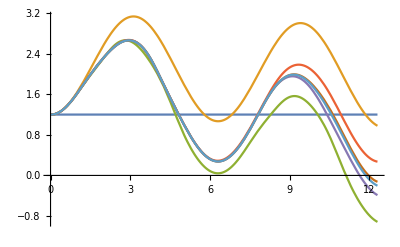

```mathematica
Clear[f,t,y]
f[t_,y_]:= Sin[t] -0.1y+ 0.1 Sin[y^2]
y0=1.2;
TMax=12.3;
y[0][t_]:=y0
TableForm[Table[
y[i]=NDSolveValue[{y[i]'[t]==f[t,y[i-1][t]],y[i][0]==y0},y[i],{t,0,TMax}],
{i,1,6}]
];
Plot[{y[0][t],y[1][t],y[2][t],y[3][t],y[4][t],y[5][t],y[6][t]},{t,0, TMax}]
```

## Series Solution

```mathematica
f[t_,y_]:= t + y^2
eq[0]=y'[t]==f[t,y[t]]
TableForm[Table[
eq[i]=D[eq[i-1],t],
{i,1,6}]
]
```

y'[t]==t+y[t]^2

y''[t]==1+2 y[t] y'[t]
y^(3)[t]==2 y'[t]^2+2 y[t] y''[t]
y^(4)[t]==6 y'[t] y''[t]+2 y[t] y^(3)[t]
y^(5)[t]==6 y''[t]^2+8 y'[t] y^(3)[t]+2 y[t] y^(4)[t]
y^(6)[t]==20 y''[t] y^(3)[t]+10 y'[t] y^(4)[t]+2 y[t] y^(5)[t]
y^(7)[t]==20 (y^(3)[t])^2+30 y''[t] y^(4)[t]+12 y'[t] y^(5)[t]+2 y[t] y^(6)[t]

## Series Solution

```mathematica
f[t_,y_]:= t + y^2
y0=1.2;
y[0][t_]:=y0
TableForm[Table[
y[i][t_]=Expand[y0+Integrate[f[τ,y[i-1][τ]],{τ,0, t}]],
{i,1,6}]
]
```

## Break

```mathematica
SetDirectory["C:\\Users\\struther\\Desktop"]
Export["Clock.gif",Table[
Graphics[{LightGreen,EdgeForm[Red],Disk[{0,0},1],Blue,Arrow[{{0,0},{Cos[θ],Sin[θ]}}]}],
{θ,0, 2π, π/24}]]
```

C:\Users\struther\Desktop

Clock.gif

```mathematica
ListAnimate[Import["Clock.gif"]]
```